# Graph Distance

We describe the graph distance, the smallest number of edges needed to travel from one vertex to the next.

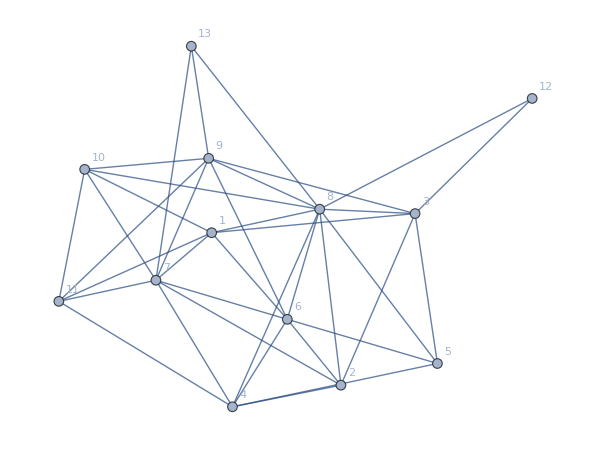

```mathematica
G=RandomGraph[{13,Floor[Binomial[15,2]/2]-15},VertexLabels->Automatic]
```

```mathematica
GraphDistance[G,12,11]
```

3

## Edge Cases: Connectivity and Graph Distance

If the graph is not connected, then there are two vertices such that there is no path between them. The graph distance is not-well defined. Or we can consider the distance to be infinite.

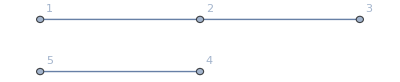

```mathematica
disconnectedGraph = UndirectedGraph[{1->2,2->3, 4->5},VertexLabels->Automatic]
```

```mathematica
GraphDistance[disconnectedGraph,1,3]
```

2

```mathematica
GraphDistance[disconnectedGraph,1,5]
```

∞

```mathematica
GraphDiameter[disconnectedGraph]
```

∞

Another weird case is the distance from a vertex to itself. Technically, the vertex itself is a path with no edges to itself, so the distance from any vertex to itself is 0.

```mathematica
GraphDistance[disconnectedGraph,1,1]
```

0

## Properties of Graph Distance

In mathematics, a ‘distance’ is usually formalized by the following three requirements:
1.) distance(x,x)=0 for all x
2.) distance(x,y)=distance(y,x)>=0 for all x,y.
3.) For all x,y if distance(x,y)=0, then x=y.
4.) For all x,y,z distance(x,y)+distance(y,z)<=distance(x,z)

The graph distance satisfies these properties.

## Diameter

The diameter of a graph is the largest distance between any two vertices.

```mathematica
GraphDiameter[G]
```

3

## Key properties of shortest paths.

Here are two simple properties of shortest paths that can serve as key lemmas to demonstrating that the graph distance satisfies the distance properties.
-If G is a graph, x and y are vertices of G, and P is a shortest path from x to y, then any sub-path of P is a shortest path between its endpoints. (optimal substructure property)
-If P is a shortest path, then P does not repeat any vertices.

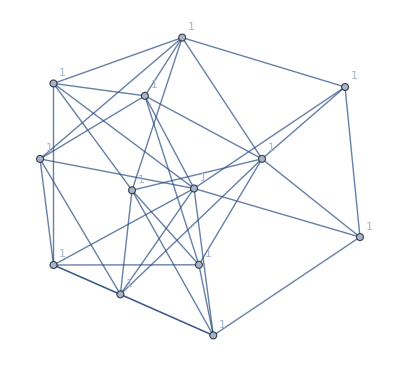

```mathematica
Graph[G,VertexLabels->GraphDistance[G,1]]
```

```mathematica
GraphDistance[G,1]
```

{0,1,2,1,1,2,1,2,2,1,2,1,1}